```mathematica
(************************Program Mahdi Molavi************************)
(********* git hub : https://github.com/mahdipc/mathematica*************)
```

```mathematica
Remove["Global`*"];
Clear["Global`*"];
𝓉[Ι_]:=Module[{i=Ι+1},
If[i==1,Return[0]];
If[i== n+1,Return[1]];
Return[1/2((2 v[v]⟦i⟧-(v[v]⟦n+1⟧+v[v]⟦1⟧))/(v[v]⟦n+1⟧-v[v]⟦1⟧)+1)];
];
τ[Ι_]:=Module[{i=Ι+1},
If[i== 1,Return[0];];
If[i==k+1,Return[1];];
Return[1/2((2 χ[v]⟦i⟧-(χ[v]⟦k+1⟧+χ[v]⟦1⟧))/(χ[v]⟦k+1⟧-χ[v]⟦1⟧)+1)];
];
𝓉[J_,Ι_]:=Module[{i=Ι,j=J},
h=𝓉[i]-𝓉[i-1];
Return[𝓉[i-1]+τ[j] h];
];
R[Ι_,J_,T_]:=Module[{i=Ι,j=J,t=T},
Return[Product[If[l≠ j,(t-𝓉[l,i]),1],{l,0,k}]/(t-𝓉[j,i])];
];
ϕ[J_,T_]:=Module[{j=J,t=T},
Return[Product[If[l≠ j,t-τ[l],1],{l,0,k}]/Product[If[l≠ j,τ[j]-τ[l],1],{l,0,k}]];
];
ϕ[J_,Ι_,T_]:=Module[{i=Ι,j=J,t=T},
If[j==0 && i==1,
Return[Piecewise[{{ϕ[0,(t-𝓉[0])/(𝓉[1]-𝓉[0])],𝓉[0]≤ t≤ 𝓉[1]}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,
Return[Piecewise[{{ϕ[j,(t-𝓉[i-1])/(𝓉[i]-𝓉[i-1])],𝓉[i-1]≤ t≤ 𝓉[i]}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{ϕ[k,(t-𝓉[n-1])/(𝓉[n]-𝓉[n-1])],𝓉[n-1]≤ t≤ 𝓉[n]}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{
{ϕ[k,(t-𝓉[i-1])/(𝓉[i]-𝓉[i-1])],𝓉[i-1]≤ t≤ 𝓉[i]},
{ϕ[0,(t-𝓉[i])/(𝓉[i+1]-𝓉[i])],𝓉[i]≤ t≤ 𝓉[i+1]}},
0]];
];
];
ψ[J_,Ι_,T_]:=Module[{i=Ι,j=J,t=T},
If[j==0&& i==1,
Return[Piecewise[{{1,0≤ t≤ 𝓉[1,1]/2}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,
Return[Piecewise[{{1,(𝓉[j-1,i]+𝓉[j,i])/2≤ t≤ (𝓉[j,i]+𝓉[j+1,i])/2}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{{1,(𝓉[k-1,i]+𝓉[k,i])/2≤ t≤ (𝓉[0,i+1]+𝓉[1,i+1])/2}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{1,(𝓉[k-1,n]+𝓉[k,n])/2≤ t≤ 1}},0]];
];
];
(*****************************)
AK[s_,t_]=(ⅇ^t Sin[t])/(1+s^2);
AF[t_]=t^3+1/2 ⅇ^t(-1+Log[2])Sin[t];
Ax[t_]=t^3;
(*****************************)
k=Input["k= "];
n=Input["n= "];
Ν=n k+1;
ν[v_]=Sort[v/.N[Solve[ChebyshevT[ n+1,v]==0,v,Reals]],Less];
χ[V_]=Sort[v/.N[Solve[ChebyshevU[k+1,v]==0,v,Reals]],Less];
d[t_]=Simplify[Join[{ψ[0,1,t]},Flatten[Table[ψ[j,i,t],{j,1,k},{i,1,n}]]]];
b[t_]=Simplify[Join[{ϕ[0,1,t]},Flatten[Table[ϕ[j,i,t],{j,1,k},{i,1,n}]]]];
VC=Table[Subscript[c, i],{i,1,Ν}];
```

```mathematica
B=ParallelTable[N[∫_0^1 b[t]⟦i⟧d[t]⟦j⟧ⅆt],{j,1,Ν},{i,1,Ν}];
Kk=ParallelTable[N[∫_0^1 ∫_0^1 AK[s,t]b[s]⟦i⟧d[t]⟦j⟧ⅆs ⅆt ],{j,1,Ν},{i,1,Ν}];
F=ParallelTable[N[∫_0^1 AF[t]d[t]⟦i⟧ⅆt],{i,1,Ν}];
VC=Inverse[B-Kk].F;
(*x[t_]=Simplify[∫_0^1 AK[s,t]Simplify[∑_(i=1)^Ν VC⟦i⟧b[s]⟦i⟧]ⅆs+AF[t]];*)
x[t_]=Simplify[∑_(i=1)^Ν VC⟦i⟧b[t]⟦i⟧];
Print["x_n(t)= ",x[t]];
```

x_n(t)= Piecewise[{{0., t>1||t<0}, {-0.18896+0.889867 t, True}}]

error=2.99093×10^-1

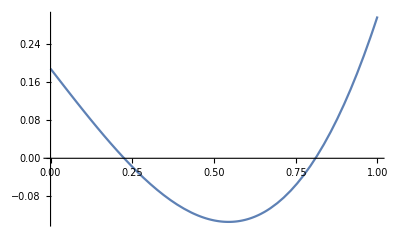

```mathematica
Print["error=",ScientificForm[Norm[Flatten[Table[Ax[𝓉[j,i]]-x[𝓉[j,i]],{i,1,n},{j,0,k}]],Infinity]]]
Plot[{Ax[t]-x[t]},{t,0,1}]
```